```mathematica
S[z_]:=z^2/2+Log[z]-X z
```

```mathematica
Solve[S'[z]==0]
```

{{X→(1+z^2)/z}}

```mathematica
zcr:=1/4 (1+ⅈ √15)
```

```mathematica
X:=1/2
```

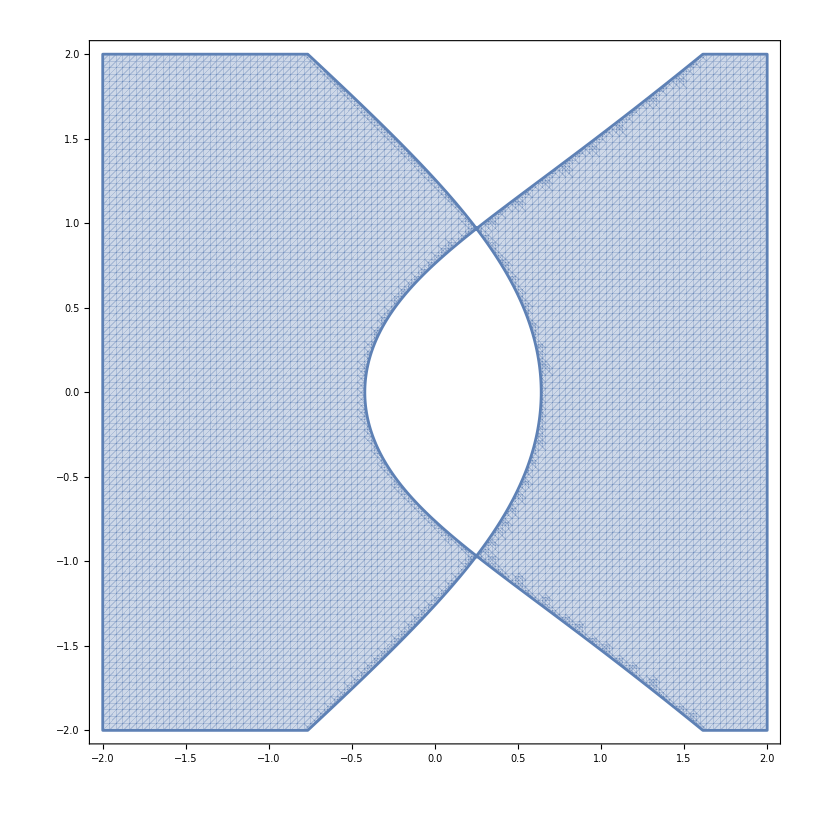

```mathematica
RegionPlot[Re[S[x+I y]]-Re[S[zcr]]>0,{x,-2,2},{y,-2,2},PlotPoints->100]
```

```mathematica
Plot3D[Re[S[x+I y]],{x,-2,2},{y,-2,2},PlotPoints->100,Exclusions->None,ViewVertical->{0,0,1},ViewPoint->{2,-3,1/2},ImageSize->600,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leo/Homepage/rmt25/rmt25-notes/pictures

```mathematica
Export["ReS_imaginary_3D.pdf",Plot3D[Re[S[x+I y]],{x,-2,2},{y,-2,2},PlotPoints->100,Exclusions->None,ViewVertical->{0,0,1},ViewPoint->{2,-3,1/2},ImageSize->600,AxesLabel->Automatic]]
```

ReS_imaginary_3D.pdf